```mathematica
(*DM SELF WD*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
clight=3 10^8;(*m/sec*)
vrel=vesc/clight;
```

```mathematica
s[r_,z_]:=(r^2*(vrel^2+r^2))/((vrel^2*z+r^2)^2)
```

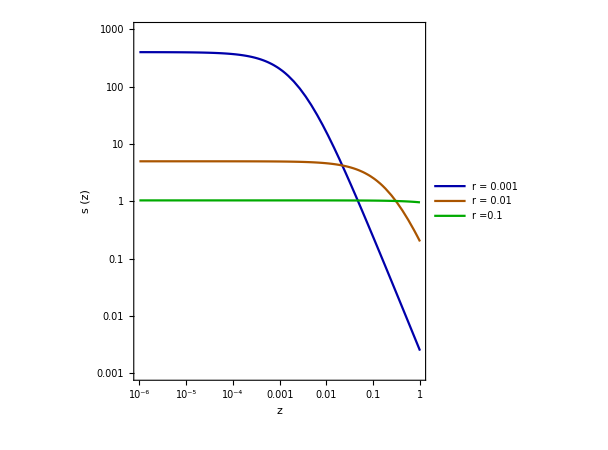

```mathematica
LogLogPlot[{s[0.001,z],s[0.01,z],s[0.1,z]},{z,10^-6,1},ImageSize->450, Frame->True,AspectRatio->1,PlotRange->{{10^-6,1},{10^-3,10^3}},PlotStyle->{Darker[Blue],Darker[Orange],Darker[Green]},FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["z",FontSize->20],Style["s (z)",FontSize->20]},PlotLegends->Placed[LineLegend[{"r = 0.001","r = 0.01","r =0.1"},LabelStyle->{FontSize->16}],{0.20,0.2}]]
```

```mathematica
Export["general_wd.pdf",-Graphics-];
```

```mathematica
(*DM SELF NS*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
clight=3 10^8;(*m/sec*)
vrel=vesc/clight;
```

```mathematica
s[r_,z_]:=(r^2*(vrel^2+r^2))/((vrel^2*z+r^2)^2)
```

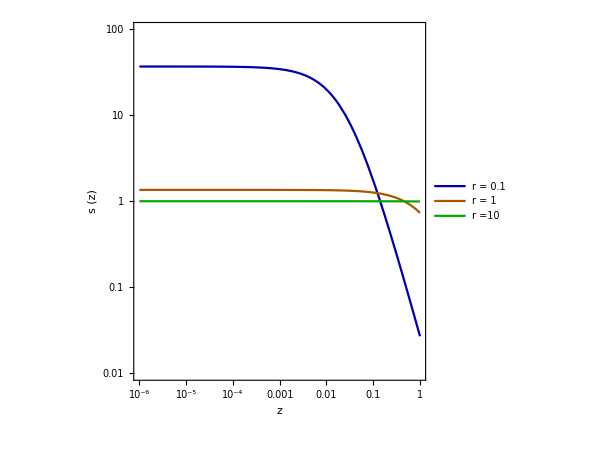

```mathematica
LogLogPlot[{s[0.1,z],s[1,z],s[10,z]},{z,10^-6,1},ImageSize->450, Frame->True,AspectRatio->1,PlotRange->{{10^-6,1},{10^-2,10^2}},PlotStyle->{Darker[Blue],Darker[Orange],Darker[Green]},FrameStyle->Directive[14, "Times",Black,Thickness[0.003]],FrameLabel->{Style["z",FontSize->20],Style["s (z)",FontSize->20]},PlotLegends->Placed[LineLegend[{"r = 0.1","r = 1","r =10"},LabelStyle->{FontSize->16}],{0.20,0.2}]]
```

```mathematica
Export["general_ns.pdf",-Graphics-];
```

```mathematica
Integrate[Sin[θ]/((a^2*Sin[θ/2]^2+b^2)^2),{θ,0,π}]
```

2/(b^2 (a^2+b^2))

```mathematica
(*DM NUCLEON NS*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
clight=3 10^8;(*m/sec*)
vrel=vesc/clight;
```

```mathematica
myticks={{{{0.01,"0.01",{0.020,0}},{0.02,"",{0.010,0}},{0.03,"",{0.010,0}},{0.04,"",{0.010,0}},{0.05,"",{0.010,0}},{0.06,"",{0.010,0}},{0.07,"",{0.010,0}},{0.08,"",{0.010,0}},{0.09,"",{0.010,0}},{0.1,"0.1",{0.020,0}},{0.2,"",{0.010,0}},{0.3,"",{0.010,0}},{0.4,"",{0.010,0}},{0.5,"",{0.010,0}},{0.6,"",{0.010,0}},{0.7,"",{0.010,0}},{0.8,"",{0.010,0}},{0.9,"",{0.010,0}},{1,"1",{0.020,0}},{2,"",{0.010,0}},{3,"",{0.010,0}},{4,"",{0.010,0}},{5,"",{0.010,0}},{6,"",{0.010,0}},{7,"",{0.010,0}},{8,"",{0.010,0}},{9,"",{0.010,0}},{10,"10",{0.020,0}},{20,"",{0.010,0}},{30,"",{0.010,0}},{40,"",{0.010,0}},{50,"",{0.010,0}},{60,"",{0.010,0}},{70,"",{0.010,0}},{80,"",{0.010,0}},{90,"",{0.010,0}},{100,"100",{0.020,0}}},None},{{{10^-6,"10^-6",{0.020,0}},{2*10^-6,"",{0.010,0}},{3*10^-6,"",{0.010,0}},{4*10^-6,"",{0.010,0}},{5*10^-6,"",{0.010,0}},{6*10^-6,"",{0.010,0}},{7*10^-6,"",{0.010,0}},{8*10^-6,"",{0.010,0}},{9*10^-6,"",{0.010,0}},{10^-5,"10^-5",{0.020,0}},{2*10^-5,"",{0.010,0}},{3*10^-5,"",{0.010,0}},{4*10^-5,"",{0.010,0}},{5*10^-5,"",{0.010,0}},{6*10^-5,"",{0.010,0}},{7*10^-5,"",{0.010,0}},{8*10^-5,"",{0.010,0}},{9*10^-5,"",{0.010,0}},{10^-4,"10^-4",{0.020,0}},{2*10^-4,"",{0.010,0}},{3*10^-4,"",{0.010,0}},{4*10^-4,"",{0.010,0}},{5*10^-4,"",{0.010,0}},{6*10^-4,"",{0.010,0}},{7*10^-4,"",{0.010,0}},{8*10^-4,"",{0.010,0}},{9*10^-4,"",{0.010,0}},{10^-3,"10^-3",{0.020,0}},{2*10^-3,"",{0.010,0}},{3*10^-3,"",{0.010,0}},{4*10^-3,"",{0.010,0}},{5*10^-3,"",{0.010,0}},{6*10^-3,"",{0.010,0}},{7*10^-3,"",{0.010,0}},{8*10^-3,"",{0.010,0}},{9*10^-3,"",{0.010,0}},{10^-2,"10^-2",{0.020,0}},{2*10^-2,"",{0.010,0}},{3*10^-2,"",{0.010,0}},{4*10^-2,"",{0.010,0}},{5*10^-2,"",{0.010,0}},{6*10^-2,"",{0.010,0}},{7*10^-2,"",{0.010,0}},{8*10^-2,"",{0.010,0}},{9*10^-2,"",{0.010,0}},{10^-1,"10^-1",{0.020,0}},{0.2,"",{0.010,0}},{0.3,"",{0.010,0}},{0.4,"",{0.010,0}},{0.5,"",{0.010,0}},{0.6,"",{0.010,0}},{0.7,"",{0.010,0}},{0.8,"",{0.010,0}},{0.9,"",{0.010,0}},{1,"1",{0.020,0}}},None}};
```

```mathematica
s[r_,z_]:=(r^2*(vrel^2+r^2))/((vrel^2*z+r^2)^2);
```

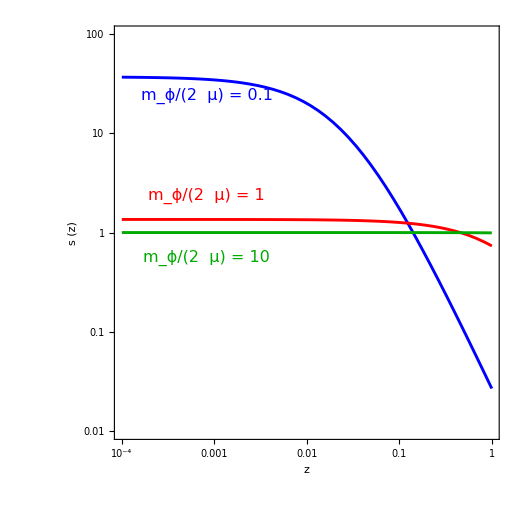

```mathematica
p=LogLogPlot[{s[0.1,z],s[1,z],s[10,z]},{z,10^-4,1},ImageSize->520, Frame->True,AspectRatio->1,PlotRange->{{10^-4,1},{10^-2,10^2}},PlotStyle->{{Blue,Thickness[0.004]},{Red,Thickness[0.004]},{Darker[Green],Thickness[0.004]}},FrameStyle->Directive[14, "Times",Black,Thickness[0.0025]],FrameLabel->{Style["z",FontSize->20,FontSlant->Italic],Style["s (z)",FontSize->20,FontSlant->Italic]},FrameTicksStyle->Directive[Black],FrameTicks->myticks,Epilog->{Text[Style["m_ϕ/(2  μ) = 0.1",Blue,16,FontFamily->"Times"],Scaled[{.24,.83}]],Text[Style["m_ϕ/(2  μ) = 1",Red,16,FontFamily->"Times"],Scaled[{.24,.59}]],Text[Style["m_ϕ/(2  μ) = 10",Darker[Green],16,FontFamily->"Times"],Scaled[{.24,.44}]]}]
```

```mathematica
Export["general_ns.pdf",p];
```

```mathematica
(*PlotLegends->Placed[LineLegend[{"r = 0.1","r = 1","r =10"},LabelStyle->{FontSize->16}],{0.20,0.2}]*)
```

```mathematica
NIntegrate[p[100.,100,z],{z,0,1}]//Quiet
```

1.

```mathematica
(*Integrate[p[m,z],{z,zmin,1},Assumptions->zmin<1&&m>0&&a>0]*)
```

```mathematica
g1[m_,mx_,u_]:=(m^2 vesc^2)/(vesc^2+u^2)1/(m^2+2a[mx](1-vesc^2/(vesc^2+u^2)))
```

```mathematica
fMB[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2];
```

```mathematica
Cself[m_,mx_,sigmaself_,Nchi_]:=ρx/mx sigmaself Nchi m^2 vesc^2 NIntegrate[fMB[u]/u 1/((m^2+mx^2 vrel^2)-(mx^2 vrel^2 vesc^2)/(vesc^2+u^2)),{u,0,Infinity}]
```